## Steady state of the quantum clock with athermal resources

```mathematica
Clear[H0,r0,Ω ,ω,gamma,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];KroneckerProduct[{{1/Sqrt[2]},{0},{-1/Sqrt[2]}},{1/Sqrt[2],0,-1/Sqrt[2]}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi/2;phi=0;gw=3;g0=4;dt=0.01;gamma=3;Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];Lw=KroneckerProduct[{{0},{1},{0}},{1,0,0}];Lwd=KroneckerProduct[{{1},{0},{0}},{0,1,0}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
For[n=0,n<10000+1,n++,rho[0]=r0;
rho[n+1]=(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gw(Lw.rho[n].Lwd-1/2(rho[n].Lwd.Lw+Lwd.Lw.rho[n]))+g0(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))));]
```

```mathematica
Clear[H0,r0,Ω ,ω,gamma,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi/2;phi=0;gw=3;g0=4;dt=0.01;gamma=3;oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
For[n=0,n<10000+1,n++,rho1[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
rho1[n+1]=Mg0.(M0.(rho1[n]+dt(-I (H0.rho1[n]-rho1[n].H0)-gamma(oX.(oX.rho1[n]-rho1[n].oX)-(oX.rho1[n]-rho1[n].oX).oX))).Transpose[M0]).Transpose[Mg0]+Mg1.(M0.(rho1[n]+dt(-I (H0.rho1[n]-rho1[n].H0)-gamma(oX.(oX.rho1[n]-rho1[n].oX)-(oX.rho1[n]-rho1[n].oX).oX))).Transpose[M0]).Transpose[Mg1]+Mg0.(M1.(rho1[n]+dt(-I (H0.rho1[n]-rho1[n].H0)-gamma(oX.(oX.rho1[n]-rho1[n].oX)-(oX.rho1[n]-rho1[n].oX).oX))).Transpose[M1]).Transpose[Mg0]+Mg1.(M1.(rho1[n]+dt(-I (H0.rho1[n]-rho1[n].H0)-gamma(oX.(oX.rho1[n]-rho1[n].oX)-(oX.rho1[n]-rho1[n].oX).oX))).Transpose[M1]).Transpose[Mg1];]
```

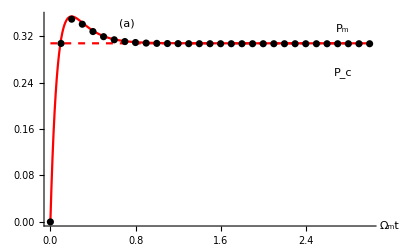

```mathematica
pmm=Show[Plot[(2 g0 gamma (8 gamma gw+gw^2+4 Ω^2) Sin[theta]^2)/(gw (8 gamma+gw) (6 g0 gamma+(g0+gamma) gw)+4 (2 g0 gamma+(g0+gamma) gw) Ω^2+gamma ((2 g0-gw) gw (8 gamma+gw)-4 (2 g0+gw) Ω^2) Cos[2 theta]),{n,0, 300 dt},PlotStyle->{Red,Dashed},PlotRange->All,BaseStyle->{Black,FontSize->20},AxesLabel->{Style["Ω_mt",Italic,24,Black]},Epilog->{{Style[Text["P_m",Scaled[{0.9,0.92}]],16,Red]},{Style[Text["(a)",Scaled[{0.25,0.95}]],16,Black]},{Style[Text["P_c",Scaled[{0.9,0.72}]],16,Blue]}}],ListPlot[{Table[{ n dt,Tr[rho[n].KroneckerProduct[{{1},{0},{0}},{1,0,0}]]},{n,0,300}]},Joined->True,PlotRange->All,PlotStyle->{Red}],ListPlot[{Table[{ n dt,Tr[rho1[n].KroneckerProduct[{{1},{0},{0}},{1,0,0}]]},{n,0,300,10}]},PlotRange->All,PlotStyle->{Black,PointSize[0.015]}]]
```

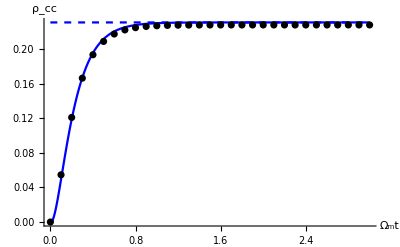

```mathematica
pcc=Show[Plot[-(2 gamma gw (8 gamma gw+gw^2+4 Ω^2) Sin[theta]^2)/(-gw (8 gamma+gw) (6 g0 gamma+(g0+gamma) gw)-4 (2 g0 gamma+(g0+gamma) gw) Ω^2+gamma (-(2 g0-gw) gw (8 gamma+gw)+4 (2 g0+gw) Ω^2) Cos[2 theta]),{n,0,300 dt},PlotStyle->{Blue,Dashed},PlotRange->All,BaseStyle->{Black,FontSize->20},AxesLabel->{Style["Ω_mt",Italic,24,Black],Style["ρ_cc",Italic,24,Black]}],ListPlot[{Table[{ n dt,Tr[rho[n].KroneckerProduct[{{0},{1},{0}},{0,1,0}]]},{n,0,300}]},Joined->True,PlotRange->All,PlotStyle->{Blue}],ListPlot[{Table[{ n dt,Tr[rho1[n].KroneckerProduct[{{0},{1},{0}},{0,1,0}]]},{n,0,300,10}]},PlotRange->All,PlotStyle->{Black,PointSize[0.015]}]]
```

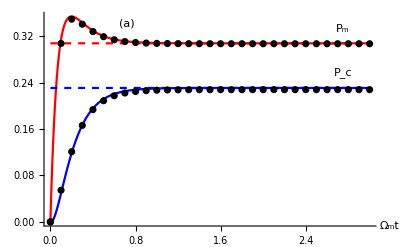

```mathematica
pad=Show[pmm,pcc]
```

```mathematica
gw=3;gamma=.;g0=4;t4=Table[{gamma,ct={};ct1={};Do[For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
M[n]=RandomChoice[{Chop[Tr[M0.rho[n].M0]],1-Chop[Tr[M0.rho[n].M0]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=Mg0.(M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]/Tr[M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]]).Transpose[Mg0]+Mg1.(M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]/Tr[M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]]).Transpose[Mg1];
];AppendTo[ct,Mean[Table[count[n],{n,0,1000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,1000}]]];,{1000}];Mean[ct],Mean[ct1]},{gamma,1,10,1}]
```

```mathematica
t4={{1,0.006942057942057943,0.006896767232767233},{2,0.008570429570429573,0.008500747252747253},{3,0.009386613386613387,0.009302563436563433},{4,0.009764235764235766,0.009672767232767231},{5,0.009886113886113886,0.009792789210789209},{6,0.01010889110889111,0.010011136863136863},{7,0.010228771228771227,0.010128513486513486},{8,0.010353646353646355,0.010250445554445554},{9,0.0104005994005994,0.0102968991008991},{10,0.010471528471528473,0.01036610789210789}}
```

{{1,0.00694206,0.00689677},{2,0.00857043,0.00850075},{3,0.00938661,0.00930256},{4,0.00976424,0.00967277},{5,0.00988611,0.00979279},{6,0.0101089,0.0100111},{7,0.0102288,0.0101285},{8,0.0103536,0.0102504},{9,0.0104006,0.0102969},{10,0.0104715,0.0103661}}

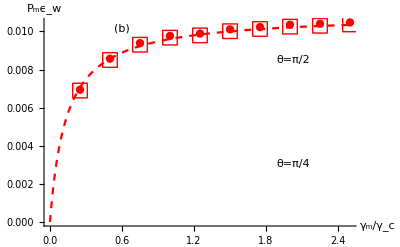

```mathematica
theta=Pi/2;pwa=Show[Plot[(gw (2 g0 g0 gamma (8 g0 gamma gw+gw^2+4 Ω^2) Sin[theta]^2)/(gw (8 g0 gamma+gw) (6 g0 g0 gamma+(g0+g0 gamma) gw)+4 (2 g0 g0 gamma+(g0+g0 gamma) gw) Ω^2+g0 gamma ((2 g0-gw) gw (8 g0 gamma+gw)-4 (2 g0+gw) Ω^2) Cos[2 theta])dt),{gamma,0,10/g0},PlotStyle->{Red,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_m/γ_c",Italic,24,Black],Style["P_mϵ_w",Italic,24,Black]},PlotRange->All,Epilog->{{Style[Text["θ=π/2",Scaled[{0.8,0.8}]],16,Red]},{Style[Text["(b)",Scaled[{0.25,0.95}]],16,Black]},{Style[Text["θ=π/4",Scaled[{0.8,0.3}]],16,Blue]}}],ListPlot[Table[{t4[[i]][[1]]/g0,t4[[i]][[2]]},{i,1,Length[t4]}],PlotStyle->{Red,PointSize[0.015]}],ListPlot[Table[{t4[[i]][[1]]/g0,t4[[i]][[3]]},{i,1,Length[t4]}],PlotRange->All, PlotMarkers->{"□",15},PlotStyle->{Red}]]
```

```mathematica
gw=3;gamma=.;g0=4;theta=Pi/4;oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];t42=Table[{gamma,ct={};ct1={};Do[For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
M[n]=RandomChoice[{Chop[Tr[M0.rho[n].M0]],1-Chop[Tr[M0.rho[n].M0]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=Mg0.(M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]/Tr[M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]]).Transpose[Mg0]+Mg1.(M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]/Tr[M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]]).Transpose[Mg1];
];AppendTo[ct,Mean[Table[count[n],{n,0,1000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,1000}]]];,{1000}];Mean[ct],Mean[ct1]},{gamma,1,10,1}]
```

$Aborted

```mathematica
t42={{1,0.0031728271728271727,0.0031632447552447543},{2,0.0037822177822177823,0.00376838961038961},{3,0.004105894105894106,0.004089304695304696},{4,0.004142857142857143,0.004125694305694307},{5,0.004281718281718282,0.004263868131868132},{6,0.0043906093906093905,0.004371422577422578},{7,0.004377622377622378,0.0043586553446553445},{8,0.004242757242757243,0.004225142857142857},{9,0.004394605394605394,0.0043759220779220785},{10,0.004454545454545453,0.004434849150849152}}
```

{{1,0.00317283,0.00316324},{2,0.00378222,0.00376839},{3,0.00410589,0.0040893},{4,0.00414286,0.00412569},{5,0.00428172,0.00426387},{6,0.00439061,0.00437142},{7,0.00437762,0.00435866},{8,0.00424276,0.00422514},{9,0.00439461,0.00437592},{10,0.00445455,0.00443485}}

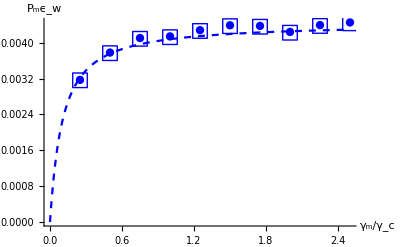

```mathematica
theta=Pi/4;pwb=Show[Plot[(gw (2 g0 g0 gamma (8 g0 gamma gw+gw^2+4 Ω^2) Sin[theta]^2)/(gw (8 g0 gamma+gw) (6 g0 g0 gamma+(g0+g0 gamma) gw)+4 (2 g0 g0 gamma+(g0+g0 gamma) gw) Ω^2+g0 gamma ((2 g0-gw) gw (8 g0 gamma+gw)-4 (2 g0+gw) Ω^2) Cos[2 theta])dt),{gamma,0,10/g0},PlotStyle->{Blue,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_m/γ_c",Italic,24,Black],Style["P_mϵ_w",Italic,24,Black]},PlotRange->All],ListPlot[Table[{t42[[i]][[1]]/g0,t42[[i]][[2]]},{i,1,Length[t42]}],PlotStyle->{Blue,PointSize[0.015]}],ListPlot[Table[{t42[[i]][[1]]/g0,t42[[i]][[3]]},{i,1,Length[t42]}],PlotRange->All, PlotMarkers->{"□",15},PlotStyle->{Blue}]]
```

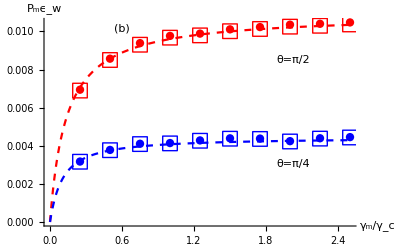

```mathematica
pat=Show[pwa,pwb]
```

```mathematica
gw=3;gamma=.;g0=4;theta=Pi/3;oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];t43=Table[{gamma,ct={};ct1={};Do[For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
M[n]=RandomChoice[{Chop[Tr[M0.rho[n].M0]],1-Chop[Tr[M0.rho[n].M0]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=Mg0.(M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]/Tr[M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]]).Transpose[Mg0]+Mg1.(M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]/Tr[M[n].(rho[n]+dt(-I (H0.rho[n]-rho[n].H0)-gamma(oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX))).Transpose[M[n]]]).Transpose[Mg1];
];AppendTo[ct,Mean[Table[count[n],{n,0,1000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,1000}]]];,{1000}];Mean[ct],Mean[ct1]},{gamma,1,10,1}]
```

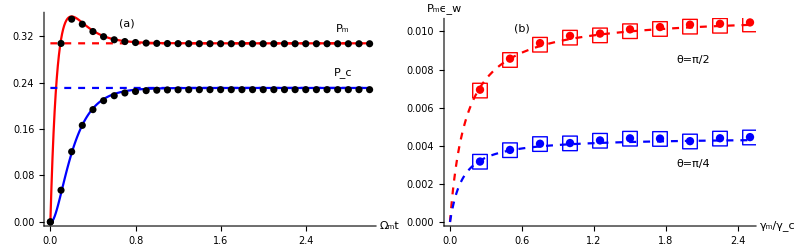

```mathematica
GraphicsGrid[{{pad,pat}},Spacings->{0, 0},ImageSize->800]
```

## Simulations for hybrid quantum clocks

```mathematica
fm[theta_]:=-((ⅇ^(betac ω) gammac (-ⅇ^(2 betac ω) gammah^3-ⅇ^(betac ω+betah Ω) gammah^2 (2 gammac+ⅇ^(betac ω) (13 gamma+2 (gammah+gw)))+ⅇ^(3 betah Ω) gamma (-gammac^2-2 ⅇ^(betac ω) gammac (4 gamma+gammah+gw)-ⅇ^(2 betac ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))+ⅇ^(2 betah Ω) gammah (-gammac^2-2 ⅇ^(betac ω) gammac (7 gamma+gammah+gw)-ⅇ^(2 betac ω) ((4 gamma+gammah+gw) (10 gamma+gammah+gw)+4 Ω^2))+ⅇ^(betah Ω) gamma (ⅇ^(2 betah Ω) gammac^2+2 ⅇ^(betac ω+betah Ω) gammac (-gammah+ⅇ^(betah Ω) (4 gamma+gammah+gw))+ⅇ^(2 betac ω) (-3 gammah^2-2 ⅇ^(betah Ω) gammah (12 gamma+gammah+gw)+ⅇ^(2 betah Ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))) Cos[2 theta]))/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta]));
```

```mathematica
fmt[theta_,betah_,gamma_,gw_]:=-((ⅇ^(betac ω) gammac (-ⅇ^(2 betac ω) gammah^3-ⅇ^(betac ω+betah Ω) gammah^2 (2 gammac+ⅇ^(betac ω) (13 gamma+2 (gammah+gw)))+ⅇ^(3 betah Ω) gamma (-gammac^2-2 ⅇ^(betac ω) gammac (4 gamma+gammah+gw)-ⅇ^(2 betac ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))+ⅇ^(2 betah Ω) gammah (-gammac^2-2 ⅇ^(betac ω) gammac (7 gamma+gammah+gw)-ⅇ^(2 betac ω) ((4 gamma+gammah+gw) (10 gamma+gammah+gw)+4 Ω^2))+ⅇ^(betah Ω) gamma (ⅇ^(2 betah Ω) gammac^2+2 ⅇ^(betac ω+betah Ω) gammac (-gammah+ⅇ^(betah Ω) (4 gamma+gammah+gw))+ⅇ^(2 betac ω) (-3 gammah^2-2 ⅇ^(betah Ω) gammah (12 gamma+gammah+gw)+ⅇ^(2 betah Ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))) Cos[2 theta]))/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta]));
```

```mathematica
fc[theta_]:=-((-ⅇ^(3 betac ω) gammah^3 gw-ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+gammah+3 gw)+ⅇ^(betac ω) gw (13 gamma+2 (gammah+gw)))-ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 (gamma+gammah)+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+7 gamma (gammah+2 gw)+(gammah+gw) (gammah+2 gw))+ⅇ^(2 betac ω) gw ((4 gamma+gammah+gw) (10 gamma+gammah+gw)+4 Ω^2))+ⅇ^(3 betah Ω) (-gammac^3 (gamma+gammah+gw)-ⅇ^(betac ω) gammac^2 (8 gamma^2+2 (gammah+gw)^2+gamma (14 gammah+15 gw))-ⅇ^(3 betac ω) gamma gw ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2)-ⅇ^(2 betac ω) gammac ((gammah+gw)^3+8 gamma^2 (5 gammah+6 gw)+gamma (gammah+gw) (13 gammah+15 gw)+4 gamma Ω^2+4 (gammah+gw) Ω^2))+ⅇ^(betah Ω) gamma (ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (2 gammah-ⅇ^(betah Ω) (-8 gamma+2 gammah+gw))+ⅇ^(2 betac ω) gammac (gammah^2-2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)-ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) gw (-3 gammah^2-2 ⅇ^(betah Ω) gammah (12 gamma+gammah+gw)+ⅇ^(2 betah Ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))) Cos[2 theta])/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta]));
```

```mathematica
fct[theta_,betah_,gamma_,gw_]:=-((-ⅇ^(3 betac ω) gammah^3 gw-ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+gammah+3 gw)+ⅇ^(betac ω) gw (13 gamma+2 (gammah+gw)))-ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 (gamma+gammah)+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+7 gamma (gammah+2 gw)+(gammah+gw) (gammah+2 gw))+ⅇ^(2 betac ω) gw ((4 gamma+gammah+gw) (10 gamma+gammah+gw)+4 Ω^2))+ⅇ^(3 betah Ω) (-gammac^3 (gamma+gammah+gw)-ⅇ^(betac ω) gammac^2 (8 gamma^2+2 (gammah+gw)^2+gamma (14 gammah+15 gw))-ⅇ^(3 betac ω) gamma gw ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2)-ⅇ^(2 betac ω) gammac ((gammah+gw)^3+8 gamma^2 (5 gammah+6 gw)+gamma (gammah+gw) (13 gammah+15 gw)+4 gamma Ω^2+4 (gammah+gw) Ω^2))+ⅇ^(betah Ω) gamma (ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (2 gammah-ⅇ^(betah Ω) (-8 gamma+2 gammah+gw))+ⅇ^(2 betac ω) gammac (gammah^2-2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)-ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) gw (-3 gammah^2-2 ⅇ^(betah Ω) gammah (12 gamma+gammah+gw)+ⅇ^(2 betah Ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))) Cos[2 theta])/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta]));
```

```mathematica
Clear[H0,r0,Ω ,ω,gamma,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi;phi=0;gw=3;dt=0.01;gamma=3;gammah=4;gammac=4;
g0=4;betah=(3/Ω);betac=100/ω;
Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];Lw=KroneckerProduct[{{0},{1},{0}},{1,0,0}];Lwd=KroneckerProduct[{{1},{0},{0}},{0,1,0}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
rho[n+1]=(M0.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M0])+(M1.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M1]);]
```

```mathematica
Clear[H0,r0,Ω ,ω,gamma,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi;phi=0;gw=3;dt=0.01;gamma=3;gammah=4;gammac=4;
g0=4;betah=(3/Ω);betac=100/ω;Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];Lw=KroneckerProduct[{{0},{1},{0}},{1,0,0}];Lwd=KroneckerProduct[{{1},{0},{0}},{0,1,0}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
For[n=0,n<1000+1,n++,rho2[0]=r0;
rho2[n+1]=(rho2[n]+dt (-I (H0.rho2[n]-rho2[n].H0)-gamma (oX.(oX.rho2[n]-rho2[n].oX)-(oX.rho2[n]-rho2[n].oX).oX)+gammah(Lh.rho2[n].Lhd-1/2(rho2[n].Lhd.Lh+Lhd.Lh.rho2[n]))+gammah Exp[-betah Ω ](Lhd.rho2[n].Lh-1/2(rho2[n].Lh.Lhd+Lh.Lhd.rho2[n]))+gw(Lw.rho2[n].Lwd-1/2(rho2[n].Lwd.Lw+Lwd.Lw.rho2[n]))+gammac(Lc.rho2[n].Lcd-1/2(rho2[n].Lcd.Lc+Lcd.Lc.rho2[n]))+gammac Exp[-betac ω ](Lcd.rho2[n].Lc-1/2(rho2[n].Lc.Lcd+Lc.Lcd.rho2[n]))));]
```

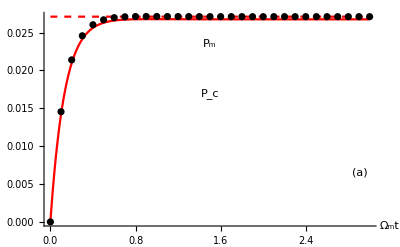

```mathematica
pmmt=Show[Plot[fm[theta],{n,0, 300 dt},PlotStyle->{Red,Dashed},PlotRange->All,BaseStyle->{Black,FontSize->20},AxesLabel->{Style["Ω_mt",Italic,24,Black]},Epilog->{{Style[Text["P_m",Scaled[{0.5,0.85}]],16,Red]},{Style[Text["(a)",Scaled[{0.95,0.25}]],16,Black]},{Style[Text["P_c",Scaled[{0.5,0.62}]],16,Blue]}}],ListPlot[{Table[{ n dt,Tr[rho[n].KroneckerProduct[{{1},{0},{0}},{1,0,0}]]},{n,0,300}]},Joined->True,PlotRange->All,PlotStyle->{Red}],ListPlot[{Table[{ n dt,Tr[rho2[n].KroneckerProduct[{{1},{0},{0}},{1,0,0}]]},{n,0,300,10}]},PlotRange->All,PlotStyle->{Black,PointSize[0.015]}]]
```

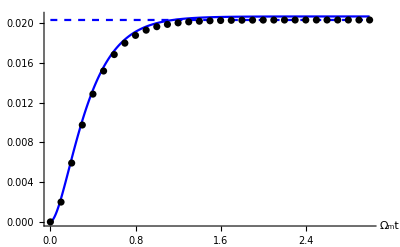

```mathematica
pcct=Show[Plot[fc[theta],{n,0, 300 dt},PlotStyle->{Blue,Dashed},PlotRange->All,BaseStyle->{Black,FontSize->20},AxesLabel->{Style["Ω_mt",Italic,24,Black]}],ListPlot[{Table[{ n dt,Tr[rho[n].KroneckerProduct[{{0},{1},{0}},{0,1,0}]]},{n,0,300}]},Joined->True,PlotRange->All,PlotStyle->{Blue}],ListPlot[{Table[{ n dt,Tr[rho2[n].KroneckerProduct[{{0},{1},{0}},{0,1,0}]]},{n,0,300,10}]},PlotRange->All,PlotStyle->{Black,PointSize[0.015]}]]
```

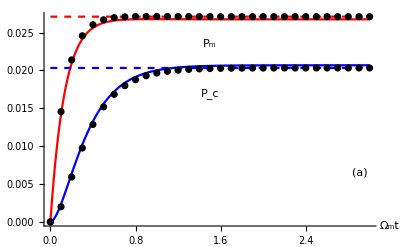

```mathematica
pta=Show[pmmt,pcct]
```

```mathematica
Clear[H0,r0,Ω ,ω,gamma,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi/4;phi=0;gw=3;dt=0.01;gamma=3;gammah=4;gammac=4;
g0=4;betah=(3/Ω);betac=100/ω;
Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];Lw=KroneckerProduct[{{0},{1},{0}},{1,0,0}];Lwd=KroneckerProduct[{{1},{0},{0}},{0,1,0}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
rho[n+1]=(M0.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M0])+(M1.(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M1]);]
```

```mathematica
Clear[H0,r0,Ω ,ω,gamma,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi/4;phi=0;gw=3;dt=0.01;gamma=3;gammah=4;gammac=4;
g0=4;betah=(3/Ω);betac=100/ω;Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];Lw=KroneckerProduct[{{0},{1},{0}},{1,0,0}];Lwd=KroneckerProduct[{{1},{0},{0}},{0,1,0}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
For[n=0,n<1000+1,n++,rho2[0]=r0;
rho2[n+1]=(rho2[n]+dt (-I (H0.rho2[n]-rho2[n].H0)-gamma (oX.(oX.rho2[n]-rho2[n].oX)-(oX.rho2[n]-rho2[n].oX).oX)+gammah(Lh.rho2[n].Lhd-1/2(rho2[n].Lhd.Lh+Lhd.Lh.rho2[n]))+gammah Exp[-betah Ω ](Lhd.rho2[n].Lh-1/2(rho2[n].Lh.Lhd+Lh.Lhd.rho2[n]))+gw(Lw.rho2[n].Lwd-1/2(rho2[n].Lwd.Lw+Lwd.Lw.rho2[n]))+gammac(Lc.rho2[n].Lcd-1/2(rho2[n].Lcd.Lc+Lcd.Lc.rho2[n]))+gammac Exp[-betac ω ](Lcd.rho2[n].Lc-1/2(rho2[n].Lc.Lcd+Lc.Lcd.rho2[n]))));]
```

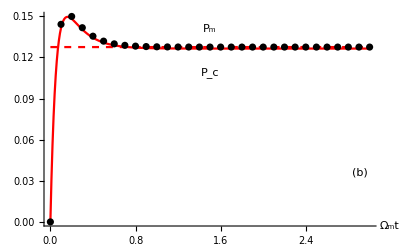

```mathematica
pmmtb=Show[Plot[fm[theta],{n,0, 300 dt},PlotStyle->{Red,Dashed},PlotRange->All,BaseStyle->{Black,FontSize->20},AxesLabel->{Style["Ω_mt",Italic,24,Black]},Epilog->{{Style[Text["P_m",Scaled[{0.5,0.92}]],16,Red]},{Style[Text["(b)",Scaled[{0.95,0.25}]],16,Black]},{Style[Text["P_c",Scaled[{0.5,0.72}]],16,Blue]}}],ListPlot[{Table[{ n dt,Tr[rho[n].KroneckerProduct[{{1},{0},{0}},{1,0,0}]]},{n,0,300}]},Joined->True,PlotRange->All,PlotStyle->{Red}],ListPlot[{Table[{ n dt,Tr[rho2[n].KroneckerProduct[{{1},{0},{0}},{1,0,0}]]},{n,0,300,10}]},PlotRange->All,PlotStyle->{Black,PointSize[0.015]}]]
```

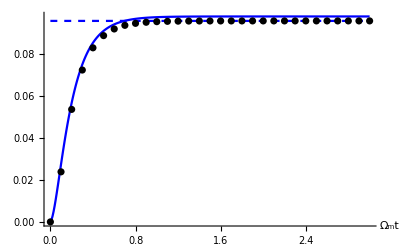

```mathematica
pcctb=Show[Plot[fc[theta],{n,0, 300 dt},PlotStyle->{Blue,Dashed},PlotRange->All,BaseStyle->{Black,FontSize->20},AxesLabel->{Style["Ω_mt",Italic,24,Black]}],ListPlot[{Table[{ n dt,Tr[rho[n].KroneckerProduct[{{0},{1},{0}},{0,1,0}]]},{n,0,300}]},Joined->True,PlotRange->All,PlotStyle->{Blue}],ListPlot[{Table[{ n dt,Tr[rho2[n].KroneckerProduct[{{0},{1},{0}},{0,1,0}]]},{n,0,300,10}]},PlotRange->All,PlotStyle->{Black,PointSize[0.015]}]]
```

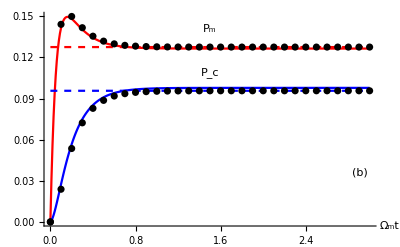

```mathematica
ptb=Show[pmmtb,pcctb]
```

```mathematica
Clear[H0,r0,Ω ,ω,gamma,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi/2;phi=0;gw=3;dt=0.01;gamma=.;gammah=4;gammac=4;
g0=4;betah=(3/Ω);betac=100/ω;Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
ta3=Table[{gamma,ct={};ct1={};Do[For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
M[n]=RandomChoice[{Chop[Tr[M0.rho[n].M0]],Max[0,1-Chop[Tr[M0.rho[n].M0]]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])/Tr[(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])];];AppendTo[ct,Mean[Table[count[n],{n,0,1000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,1000}]]];,{1000}];Mean[ct],Mean[ct1]},{gamma,1,10,1}]
```

```mathematica
ta3={{1,0.00514885114885115,0.005123932067932069},{2,0.006965034965034965,0.00691879120879121},{3,0.007841158841158841,0.00778252947052947},{4,0.008355644355644358,0.008289346653346652},{5,0.008757242757242756,0.008684185814185813},{6,0.009076923076923078,0.008998125874125872},{7,0.009320679320679322,0.009237316683316682},{8,0.009444555444555447,0.009359122877122875},{9,0.00957842157842158,0.009490607392607391},{10,0.009794205794205795,0.009701876123876123}};
```

```mathematica
fm1[gamma_,theta_]:=-((ⅇ^(betac ω) gammac (-ⅇ^(2 betac ω) gammah^3-ⅇ^(betac ω+betah Ω) gammah^2 (2 gammac+ⅇ^(betac ω) (13 gamma+2 (gammah+gw)))+ⅇ^(3 betah Ω) gamma (-gammac^2-2 ⅇ^(betac ω) gammac (4 gamma+gammah+gw)-ⅇ^(2 betac ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))+ⅇ^(2 betah Ω) gammah (-gammac^2-2 ⅇ^(betac ω) gammac (7 gamma+gammah+gw)-ⅇ^(2 betac ω) ((4 gamma+gammah+gw) (10 gamma+gammah+gw)+4 Ω^2))+ⅇ^(betah Ω) gamma (ⅇ^(2 betah Ω) gammac^2+2 ⅇ^(betac ω+betah Ω) gammac (-gammah+ⅇ^(betah Ω) (4 gamma+gammah+gw))+ⅇ^(2 betac ω) (-3 gammah^2-2 ⅇ^(betah Ω) gammah (12 gamma+gammah+gw)+ⅇ^(2 betah Ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))) Cos[2 theta]))/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta]));
```

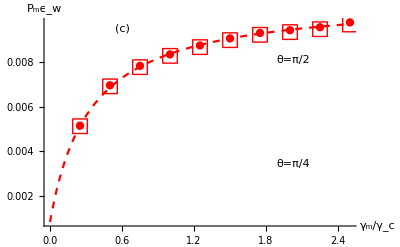

```mathematica
theta=Pi/2;pwa=Show[Plot[(gw fm1[g0 gamma,theta]dt),{gamma,0,10/g0},PlotStyle->{Red,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_m/γ_c",Italic,24,Black],Style["P_mϵ_w",Italic,24,Black]},PlotRange->All,AxesOrigin->{0,0},Epilog->{{Style[Text["θ=π/2",Scaled[{0.8,0.8}]],16,Red]},{Style[Text["(c)",Scaled[{0.25,0.95}]],16,Black]},{Style[Text["θ=π/4",Scaled[{0.8,0.3}]],16,Blue]}}],ListPlot[Table[{ta3[[i]][[1]]/g0,ta3[[i]][[2]]},{i,1,Length[ta3]}],PlotStyle->{Red,PointSize[0.015]}],ListPlot[Table[{ta3[[i]][[1]]/g0,ta3[[i]][[3]]},{i,1,Length[ta3]}],PlotRange->All, PlotMarkers->{"□",15},PlotStyle->{Red}]]
```

```mathematica
Clear[H0,r0,Ω ,ω,gammah,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi/2;phi=0;gw=3;dt=0.01;gamma=3;gammah=.;gammac=4;
g0=4;betah=(3/Ω);betac=100/ω;Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
ta31=Table[{gammah,ct={};ct1={};Do[For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
M[n]=RandomChoice[{Chop[Tr[M0.rho[n].M0]],Max[0,1-Chop[Tr[M0.rho[n].M0]]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])/Tr[(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])];];AppendTo[ct,Mean[Table[count[n],{n,0,1000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,1000}]]];,{1000}];Mean[ct],Mean[ct1]},{gammah,1,10,1}]
```

```mathematica
ta31={{1,0.008746253746253747,0.008673914085914084},{2,0.008420579420579421,0.008353204795204794},{3,0.008023976023976025,0.007962625374625375},{4,0.007806193806193807,0.007748189810189809},{5,0.007340659340659341,0.007289628371628372},{6,0.007256743256743258,0.007206885114885114},{7,0.007035964035964037,0.006989006993006994},{8,0.006827172827172827,0.0067830909090909105},{9,0.006647352647352648,0.006605328671328673},{10,0.006429570429570429,0.0063901478521478546}};
```

```mathematica
fmh[gammah_,theta_]:=-((ⅇ^(betac ω) gammac (-ⅇ^(2 betac ω) gammah^3-ⅇ^(betac ω+betah Ω) gammah^2 (2 gammac+ⅇ^(betac ω) (13 gamma+2 (gammah+gw)))+ⅇ^(3 betah Ω) gamma (-gammac^2-2 ⅇ^(betac ω) gammac (4 gamma+gammah+gw)-ⅇ^(2 betac ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))+ⅇ^(2 betah Ω) gammah (-gammac^2-2 ⅇ^(betac ω) gammac (7 gamma+gammah+gw)-ⅇ^(2 betac ω) ((4 gamma+gammah+gw) (10 gamma+gammah+gw)+4 Ω^2))+ⅇ^(betah Ω) gamma (ⅇ^(2 betah Ω) gammac^2+2 ⅇ^(betac ω+betah Ω) gammac (-gammah+ⅇ^(betah Ω) (4 gamma+gammah+gw))+ⅇ^(2 betac ω) (-3 gammah^2-2 ⅇ^(betah Ω) gammah (12 gamma+gammah+gw)+ⅇ^(2 betah Ω) ((gammah+gw) (8 gamma+gammah+gw)+4 Ω^2))) Cos[2 theta]))/(ⅇ^(3 betac ω) gammah^3 (gammac+gw)+ⅇ^(2 betac ω+betah Ω) gammah^2 (gammac (gamma+2 gammac+gammah+3 gw)+ⅇ^(betac ω) ((gammah+gw) (3 gammac+2 gw)+gamma (14 gammac+13 gw)))+ⅇ^(betac ω+2 betah Ω) gammah (gammac^2 (2 gamma+gammac+2 gammah+3 gw)+2 ⅇ^(betac ω) gammac (4 gamma^2+8 gamma gammac+7 gamma (gammah+2 gw)+(gammah+gw) (2 gammac+gammah+2 gw))+ⅇ^(2 betac ω) (14 gamma (2 gammac+gw) (gammah+gw)+(3 gammac+gw) (gammah+gw)^2+8 gamma^2 (6 gammac+5 gw)+4 (gammac+gw) Ω^2))+ⅇ^(3 betah Ω) (gammac^3 (gamma+gammah+gw)+ⅇ^(betac ω) gammac^2 (8 gamma^2+gamma (2 gammac+14 gammah+15 gw)+(gammah+gw) (gammac+2 (gammah+gw)))+ⅇ^(3 betac ω) ((gammah+gw) (8 gamma+gammah+gw) (gamma (6 gammac+gw)+gammac (gammah+gw))+4 (gamma (2 gammac+gw)+gammac (gammah+gw)) Ω^2)+ⅇ^(2 betac ω) gammac (8 gamma^2 (2 gammac+5 gammah+6 gw)+gamma (gammah+gw) (16 gammac+13 gammah+15 gw)+4 gamma Ω^2+(gammah+gw) ((gammah+gw) (2 gammac+gammah+gw)+4 Ω^2)))+ⅇ^(betah Ω) gamma (-ⅇ^(2 betah Ω) gammac^3+ⅇ^(betac ω+betah Ω) gammac^2 (-2 gammah+ⅇ^(betah Ω) (-8 gamma-2 gammac+2 gammah+gw))+ⅇ^(2 betac ω) gammac (-gammah^2+2 ⅇ^(betah Ω) gammah (-4 gamma+gammah+2 gw)+ⅇ^(2 betah Ω) ((gammah+gw) (3 gammah+gw)+8 gamma (-2 gammac+3 gammah+2 gw)-4 Ω^2))+ⅇ^(3 betac ω) (gammah^2 (2 gammac+3 gw)+2 ⅇ^(betah Ω) gammah ((2 gammac+gw) (gammah+gw)+4 gamma (2 gammac+3 gw))+ⅇ^(2 betah Ω) ((2 gammac-gw) (gammah+gw) (8 gamma+gammah+gw)-4 (2 gammac+gw) Ω^2))) Cos[2 theta]));
```

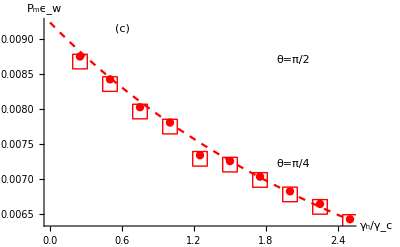

```mathematica
theta=Pi/2;pwh1=Show[Plot[(gw fmh[g0 gammah,theta]dt),{gammah,0,10/g0},PlotStyle->{Red,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_h/γ_c",Italic,24,Black],Style["P_mϵ_w",Italic,24,Black]},PlotRange->All,AxesOrigin->{0,0},Epilog->{{Style[Text["θ=π/2",Scaled[{0.8,0.8}]],16,Red]},{Style[Text["(c)",Scaled[{0.25,0.95}]],16,Black]},{Style[Text["θ=π/4",Scaled[{0.8,0.3}]],16,Blue]}}],ListPlot[Table[{ta31[[i]][[1]]/g0,ta31[[i]][[2]]},{i,1,Length[ta31]}],PlotStyle->{Red,PointSize[0.015]}],ListPlot[Table[{ta31[[i]][[1]]/g0,ta31[[i]][[3]]},{i,1,Length[ta31]}],PlotRange->All, PlotMarkers->{"□",15},PlotStyle->{Red}]]
```

```mathematica
Clear[H0,r0,Ω ,ω,gammah,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi/4;phi=0;gw=3;dt=0.01;gamma=3;gammah=.;gammac=4;
g0=4;betah=(3/Ω);betac=100/ω;Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
ta31=Table[{gammah,ct={};ct1={};Do[For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
M[n]=RandomChoice[{Chop[Tr[M0.rho[n].M0]],Max[0,1-Chop[Tr[M0.rho[n].M0]]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])/Tr[(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])];];AppendTo[ct,Mean[Table[count[n],{n,0,1000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,1000}]]];,{1000}];Mean[ct],Mean[ct1]},{gammah,1,10,1}]
```

```mathematica
ta32={{1,0.004023976023976024,0.004008291708291708},{2,0.0038631368631368633,0.0038490229770229765},{3,0.003788211788211788,0.0037746113886113885},{4,0.003816183816183816,0.0038025494505494507},{5,0.0037342657342657342,0.003721106893106893},{6,0.0036433566433566435,0.0036307972027972025},{7,0.0036103896103896107,0.003598027972027972},{8,0.00357942057942058,0.0035673486513486505},{9,0.0034645354645354647,0.003453284715284715},{10,0.0034455544455544453,0.003434271728271728}}
```

{{1,0.00402398,0.00400829},{2,0.00386314,0.00384902},{3,0.00378821,0.00377461},{4,0.00381618,0.00380255},{5,0.00373427,0.00372111},{6,0.00364336,0.0036308},{7,0.00361039,0.00359803},{8,0.00357942,0.00356735},{9,0.00346454,0.00345328},{10,0.00344555,0.00343427}}

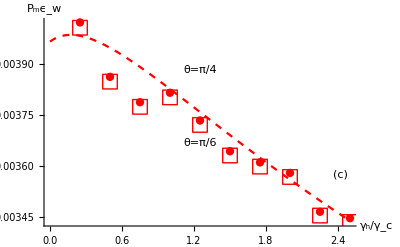

```mathematica
theta=Pi/4;pwh2=Show[Plot[(gw fmh[g0 gammah,theta]dt),{gammah,0,10/g0},PlotStyle->{Red,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_h/γ_c",Italic,24,Black],Style["P_mϵ_w",Italic,24,Black]},PlotRange->All,AxesOrigin->{0,0},Epilog->{{Style[Text["θ=π/4",Scaled[{0.5,0.75}]],16,Red]},{Style[Text["(c)",Scaled[{0.95,0.25}]],16,Black]},{Style[Text["θ=π/6",Scaled[{0.5,0.4}]],16,Blue]}}],ListPlot[Table[{ta32[[i]][[1]]/g0,ta32[[i]][[2]]},{i,1,Length[ta32]}],PlotStyle->{Red,PointSize[0.015]}],ListPlot[Table[{ta32[[i]][[1]]/g0,ta32[[i]][[3]]},{i,1,Length[ta32]}],PlotRange->All, PlotMarkers->{"□",15},PlotStyle->{Red}]]
```

```mathematica
Clear[H0,r0,Ω ,ω,gammah,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi/6;phi=0;gw=3;dt=0.01;gamma=3;gammah=.;gammac=4;
g0=4;betah=(3/Ω);betac=100/ω;Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
ta31=Table[{gammah,ct={};ct1={};Do[For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
M[n]=RandomChoice[{Chop[Tr[M0.rho[n].M0]],Max[0,1-Chop[Tr[M0.rho[n].M0]]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])/Tr[(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])];];AppendTo[ct,Mean[Table[count[n],{n,0,1000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,1000}]]];,{1000}];Mean[ct],Mean[ct1]},{gammah,1,10,1}]
```

$Aborted

```mathematica
ta33={{1,0.0020269730269730263,0.0020230229770229766},{2,0.0021048951048951046,0.0021007472527472524},{3,0.0021598401598401594,0.0021553046953046947},{4,0.0022787212787212783,0.0022736303696303693},{5,0.002243756243756243,0.0022388851148851144},{6,0.0022247752247752245,0.0022198781218781215},{7,0.002187812187812187,0.0021832447552447543},{8,0.00218081918081918,0.0021762517482517476},{9,0.0022167832167832163,0.0022121598401598393},{10,0.002218781218781218,0.0022140919080919073}}
```

{{1,0.00202697,0.00202302},{2,0.0021049,0.00210075},{3,0.00215984,0.0021553},{4,0.00227872,0.00227363},{5,0.00224376,0.00223889},{6,0.00222478,0.00221988},{7,0.00218781,0.00218324},{8,0.00218082,0.00217625},{9,0.00221678,0.00221216},{10,0.00221878,0.00221409}}

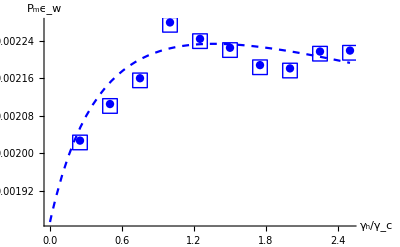

```mathematica
theta=Pi/6;pwh3=Show[Plot[(gw fmh[g0 gammah,theta]dt),{gammah,0,10/g0},PlotStyle->{Blue,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["γ_h/γ_c",Italic,24,Black],Style["P_mϵ_w",Italic,24,Black]},PlotRange->All,AxesOrigin->{0,0}],ListPlot[Table[{ta33[[i]][[1]]/g0,ta33[[i]][[2]]},{i,1,Length[ta33]}],PlotStyle->{Blue,PointSize[0.015]}],ListPlot[Table[{ta33[[i]][[1]]/g0,ta33[[i]][[3]]},{i,1,Length[ta33]}],PlotRange->All, PlotMarkers->{"□",15},PlotStyle->{Blue}]]
```

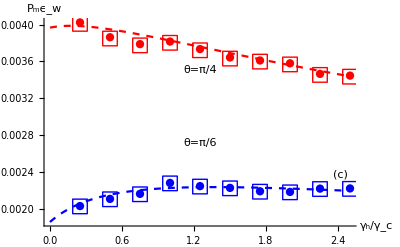

```mathematica
g3=Show[pwh2,pwh3]
```

## Thermal comparison

```mathematica
Clear[H0,r0,Ω ,ω,gammah,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi/2;phi=0;gw=3;dt=0.01;gamma=3;gammah=4;gammac=4;
g0=4;betah=.;betac=100/ω;Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
tat=Table[{betah,ct={};ct1={};Do[For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
M[n]=RandomChoice[{Chop[Tr[M0.rho[n].M0]],Max[0,1-Chop[Tr[M0.rho[n].M0]]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])/Tr[(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])];];AppendTo[ct,Mean[Table[count[n],{n,0,1000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,1000}]]];,{1000}];Mean[ct],Mean[ct1]},{betah,0,10,1}]
```

$Aborted

```mathematica
tat={{0,0.009882117882117882,0.00978906693306693},{1,0.008562437562437564,0.008492619380619381},{2,0.007905094905094907,0.007845552447552449},{3,0.007818181818181818,0.0077601398601398605},{4,0.007745254745254746,0.007688025974025974},{5,0.0077262737262737274,0.007669214785214785},{6,0.007614385614385617,0.007559208791208791},{7,0.007606393606393607,0.007551352647352649},{8,0.007543456543456544,0.007489210789210789},{9,0.007633366633366634,0.007577616383616384},{10,0.007616383616383617,0.007561242757242757}};
```

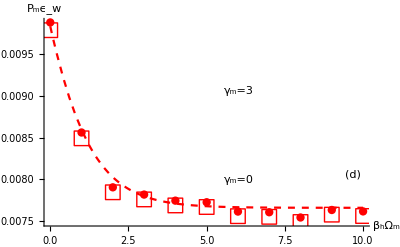

```mathematica
theta=Pi/2;pwh34=Show[Plot[(gw fmt[Pi/2,b,3,3]dt),{b,0,10},PlotStyle->{Red,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["β_hΩ_m",Italic,24,Black],Style["P_mϵ_w",Italic,24,Black]},PlotRange->All,AxesOrigin->{0,0},Epilog->{{Style[Text["γ_m=3",Scaled[{0.6,0.65}]],16,Red]},{Style[Text["(d)",Scaled[{0.95,0.25}]],16,Black]},{Style[Text["γ_m=0",Scaled[{0.6,0.22}]],16,Blue]}}],ListPlot[Table[{tat[[i]][[1]],tat[[i]][[2]]},{i,1,Length[tat]}],PlotStyle->{Red,PointSize[0.015]}],ListPlot[Table[{tat[[i]][[1]],tat[[i]][[3]]},{i,1,Length[tat]}],PlotRange->All, PlotMarkers->{"□",15},PlotStyle->{Red}]]
```

```mathematica
Clear[H0,r0,Ω ,ω,gammah,dt,gw,g0,meanc,meanv,meancv,oX,phi ,M0,M1,M0,Mg0,Mg1,M,theta];
H0=Ω KroneckerProduct[{{1},{0},{0}},{1,0,0}]+ω KroneckerProduct[{{0},{1},{0}},{0,1,0}];r0=KroneckerProduct[{{0},{0},{1}},{0,0,1}];Ω =1;ω =0.1;meanc={};meanv={};meancv={};theta=Pi/2;phi=0;gw=3;dt=0.01;gamma=0;gammah=4;gammac=4;
g0=4;betah=.;betac=100/ω;Lh=KroneckerProduct[{{0},{0},{1}},{1,0,0}];Lhd=KroneckerProduct[{{1},{0},{0}},{0,0,1}];Lc=KroneckerProduct[{{0},{0},{1}},{0,1,0}];Lcd=KroneckerProduct[{{0},{1},{0}},{0,0,1}];oX=KroneckerProduct[{{Cos[theta/2]},{0},{Sin[theta/2]Exp[-I phi]}},{Cos[theta/2],0,Sin[theta/2]Exp[I phi]}]-KroneckerProduct[{{Sin[theta/2]Exp[I phi]},{0},{-Cos[theta/2]}},{Sin[theta/2]Exp[-I phi],0,-Cos[theta/2]}];
tat1=Table[{betah,ct={};ct1={};Do[For[n=0,n<1000+1,n++,rho[0]=r0;M0={{Sqrt[1-gw dt],0,0},{0,1,0},{0,0,1}};M1={{0,0,0},{Sqrt[gw dt],0,0},{0,0,0}};Mg0={{1,0,0},{0,Sqrt[1-g0 dt],0},{0,0,1}};Mg1={{0,0,0},{0,0,0},{0,Sqrt[g0 dt],0}};
M[n]=RandomChoice[{Chop[Tr[M0.rho[n].M0]],Max[0,1-Chop[Tr[M0.rho[n].M0]]]}->{M0,M1},1][[1]];
count[n]=Abs[Tr[M[n]]/Tr[M0]-1];
rho[n+1]=(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])/Tr[(M[n].(rho[n]+dt (-I (H0.rho[n]-rho[n].H0)-gamma (oX.(oX.rho[n]-rho[n].oX)-(oX.rho[n]-rho[n].oX).oX)+gammah(Lh.rho[n].Lhd-1/2(rho[n].Lhd.Lh+Lhd.Lh.rho[n]))+gammah Exp[-betah Ω ](Lhd.rho[n].Lh-1/2(rho[n].Lh.Lhd+Lh.Lhd.rho[n]))+gammac(Lc.rho[n].Lcd-1/2(rho[n].Lcd.Lc+Lcd.Lc.rho[n]))+gammac Exp[-betac ω ](Lcd.rho[n].Lc-1/2(rho[n].Lc.Lcd+Lc.Lcd.rho[n])))).Transpose[M[n]])];];AppendTo[ct,Mean[Table[count[n],{n,0,1000}]]];AppendTo[ct1,Variance[Table[count[n],{n,0,1000}]]];,{1000}];Mean[ct],Mean[ct1]},{betah,0,10,1}]
```

```mathematica
tat1={{0,0.008455544455544457,0.00838822977022977},{1,0.004469530469530469,0.0044510889110889115},{2,0.001969030969030969,0.001965346653346653},{3,0.0007772227772227775,0.000776663336663337},{4,0.00029270729270729277,0.00029262737262737275},{5,0.00013186813186813188,0.00013186213786213786},{6,0.000037962037962037966,0.000037960039960039966},{7,0.000015984015984015985,0.000015984015984015985},{8,6.993006993006993*^-6,6.993006993006993*^-6},{9,0.,0.},{10,9.99000999000999*^-7,9.99000999000999*^-7}};
```

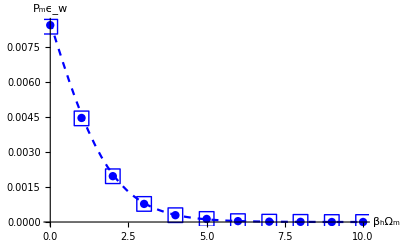

```mathematica
theta=Pi/2;pwh4=Show[Plot[(gw fmt[Pi/2,b,0,3]dt),{b,0,10},PlotStyle->{Blue,Dashed},BaseStyle->{Black,FontSize->20},AxesLabel->{Style["β_hΩ_m",Italic,24,Black],Style["P_mϵ_w",Italic,24,Black]},PlotRange->All,AxesOrigin->{0,0}],ListPlot[Table[{tat1[[i]][[1]],tat1[[i]][[2]]},{i,1,Length[tat1]}],PlotStyle->{Blue,PointSize[0.015]}],ListPlot[Table[{tat1[[i]][[1]],tat1[[i]][[3]]},{i,1,Length[tat1]}],PlotRange->All, PlotMarkers->{"□",15},PlotStyle->{Blue}]]
```

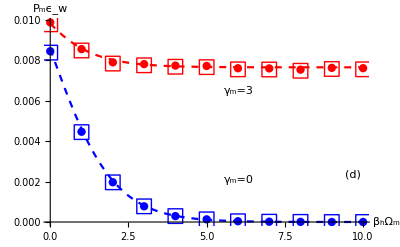

```mathematica
g4=Show[pwh34,pwh4]
```

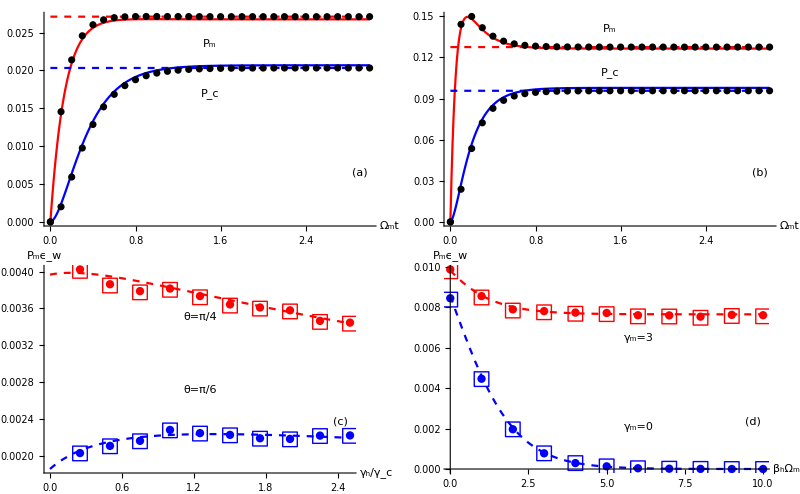

```mathematica
GraphicsGrid[{{pta,ptb},{g3,g4}},Spacings->{0, 0},ImageSize->800]
```